```mathematica
llf[c_,r_]:= c*Log[(1+Exp[-r*t])/2]+Log[(1-Exp[-r*t])/2];
```

```mathematica
ll= c*Log[(1+Exp[-r*t])/2]+Log[(1-Exp[-r*t])/2];
```

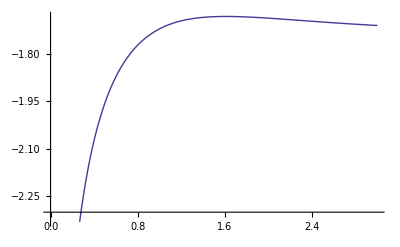

```mathematica
Plot[llf[1.5,1],{t,0,3}]
```

```mathematica
s =Normal[Series[ll,{t,0,3}]]
```

(-r/2-(c r)/2) t+1/24 (r^2+3 c r^2) t^2+Log[r/2]+Log[t]

```mathematica
CForm[s]
```

(-r/2. - (c*r)/2.)*t + ((Power(r,2) + 3*c*Power(r,2))*Power(t,2))/24. + Log(r/2.) + Log(t)

```mathematica
sd =Simplify[(s/.{t->t1}) - (s/.{t->t2})]
```

1/24 (r (t1-t2) (-12+r (t1+t2)+3 c (-4+r (t1+t2)))+24 Log[t1]-24 Log[t2])

```mathematica
rsol =Simplify[Solve[sd==d1-d2,r]][[1]]
```

{r→(2 (3 t1+3 c t1-3 t2-3 c t2+1/4 √(144 (1+c)^2 (t1-t2)^2+96 (1+3 c) (t1^2-t2^2) (d1-d2-Log[t1]+Log[t2]))))/((1+3 c) (t1^2-t2^2))}

```mathematica
forc =FullSimplify[s/.rsol]
```

Log[t]-((1+c) t (3 (1+c) t1-3 (1+c) t2+√3 √((t1-t2) (3 (1+c)^2 (t1-t2)+2 (1+3 c) (t1+t2) (d1-d2-Log[t1]+Log[t2])))))/((1+3 c) (t1-t2) (t1+t2))+((3 (1+c) t (t1-t2)+√3 t √((t1-t2) (3 (1+c)^2 (t1-t2)+2 (1+3 c) (t1+t2) (d1-d2-Log[t1]+Log[t2]))))^2)/(6 (1+3 c) (t1^2-t2^2)^2)+Log[(3 (1+c) t1-3 (1+c) t2+√3 √((t1-t2) (3 (1+c)^2 (t1-t2)+2 (1+3 c) (t1+t2) (d1-d2-Log[t1]+Log[t2]))))/((1+3 c) (t1-t2) (t1+t2))]

```mathematica
CForm[Experimental`OptimizeExpression[forc]]
```

Experimental_OptimizedExpression(Block(List(Compile_$$18724,Compile_$$18728,Compile_$$18729,Compile_$$18725,Compile_$$18726,Compile_$$18731,Compile_$$18727,Compile_$$18735,
     Compile_$$18736,Compile_$$18737,Compile_$$18738,Compile_$$18739,Compile_$$18740,Compile_$$18741,Compile_$$18742,Compile_$$18743,Compile_$$18744,Compile_$$18745,Compile_$$18746,
     Compile_$$18730,Compile_$$18732,Compile_$$18733,Compile_$$18734,Compile_$$18747,Compile_$$18748),
    (Compile_$$18724 = 1 + c,Compile_$$18728 = -t2,Compile_$$18729 = t1 + Compile_$$18728,Compile_$$18725 = 3*c,Compile_$$18726 = 1 + Compile_$$18725,Compile_$$18731 = t1 + t2,
     Compile_$$18727 = 1/Compile_$$18726,Compile_$$18735 = Sqrt(3),Compile_$$18736 = Power(Compile_$$18724,2),Compile_$$18737 = 3*Compile_$$18736*Compile_$$18729,Compile_$$18738 = -d2,
     Compile_$$18739 = Log(t1),Compile_$$18740 = -Compile_$$18739,Compile_$$18741 = Log(t2),Compile_$$18742 = d1 + Compile_$$18738 + Compile_$$18740 + Compile_$$18741,
     Compile_$$18743 = 2*Compile_$$18726*Compile_$$18731*Compile_$$18742,Compile_$$18744 = Compile_$$18737 + Compile_$$18743,Compile_$$18745 = Compile_$$18729*Compile_$$18744,
     Compile_$$18746 = Sqrt(Compile_$$18745),Compile_$$18730 = 1/Compile_$$18729,Compile_$$18732 = 1/Compile_$$18731,Compile_$$18733 = 3*Compile_$$18724*t1,
     Compile_$$18734 = -3*Compile_$$18724*t2,Compile_$$18747 = Compile_$$18735*Compile_$$18746,Compile_$$18748 = Compile_$$18733 + Compile_$$18734 + Compile_$$18747,
     Log(t) - Compile_$$18724*Compile_$$18727*t*Compile_$$18730*Compile_$$18732*Compile_$$18748 + 
      (Compile_$$18727*Power(3*Compile_$$18724*t*Compile_$$18729 + Compile_$$18735*t*Compile_$$18746,2))/(6.*Power(Power(t1,2) - Power(t2,2),2)) + 
      Log(Compile_$$18727*Compile_$$18730*Compile_$$18732*Compile_$$18748))))

```mathematica
CForm[forc]
```

Log(t) - ((1 + c)*t*(3*(1 + c)*t1 - 3*(1 + c)*t2 + Sqrt(3)*Sqrt((t1 - t2)*(3*Power(1 + c,2)*(t1 - t2) + 2*(1 + 3*c)*(t1 + t2)*(d1 - d2 - Log(t1) + Log(t2))))))/
    ((1 + 3*c)*(t1 - t2)*(t1 + t2)) + Power(3*(1 + c)*t*(t1 - t2) + Sqrt(3)*t*Sqrt((t1 - t2)*(3*Power(1 + c,2)*(t1 - t2) + 2*(1 + 3*c)*(t1 + t2)*(d1 - d2 - Log(t1) + Log(t2)))),2)/
    (6.*(1 + 3*c)*Power(Power(t1,2) - Power(t2,2),2)) + Log((3*(1 + c)*t1 - 3*(1 + c)*t2 + 
       Sqrt(3)*Sqrt((t1 - t2)*(3*Power(1 + c,2)*(t1 - t2) + 2*(1 + 3*c)*(t1 + t2)*(d1 - d2 - Log(t1) + Log(t2)))))/((1 + 3*c)*(t1 - t2)*(t1 + t2)))

```mathematica
test=forc/.{t1->0.8,t2->1,d1->-2,d2->-3,t->0.25}
```

-1.38629+(0.694444 (1+c) (-0.6-0.6 c+1/4 √(5.76 (1+c)^2-42.2718 (1+3 c))))/(1+3 c)+(0.0803755 (-0.6-0.6 c+1/4 √(5.76 (1+c)^2-42.2718 (1+3 c)))^2)/(1+3 c)+Log[-(2.77778 (-0.6-0.6 c+1/4 √(5.76 (1+c)^2-42.2718 (1+3 c))))/(1+3 c)]

```mathematica
FullSimplify[test]
```

(-1.95744+0.358796 √((-20.3284+c) (0.311823+c))+c (-5.51353-0.358796 c+0.358796 √((-20.3284+c) (0.311823+c)))+(1+3. c) Log[(1.66667+1.66667 c-1.66667 √((-20.3284+c) (0.311823+c)))/(1.+3. c)])/(1.+3. c)

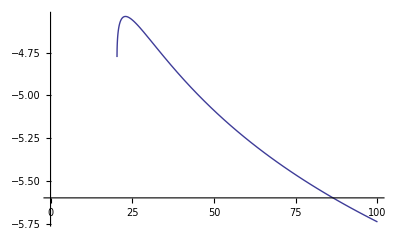

```mathematica
Plot[test,{c,0,100}]
```

```mathematica
(*traverses entire expression tree storing each node*)
AllSubExpressions[x_,accum_]:=Module[{result,i,len},len=Length[x];
result=Append[accum,x];
If[LeafCount[x]>1,For[i=1,i≤len,i++,result=ToSubExpressions2[x[[i]],result];];];
Return[Sort[result,LeafCount[#1]>LeafCount[#2]&]]]

CommonSubExpressions[statements_]:=Module[{common,subexpressions},subexpressions=AllSubExpressions[statements,{}];
(*get the unique set of sub expressions*)common=DeleteDuplicates[subexpressions];
(*remove constants from the list*)common=Select[common,LeafCount[#]>1&];
(*only keep subexpressions that occur more than once*)common=Select[common,Count[subexpressions,#]>1&];
(*output the list of possible subexpressions to replace with the number of occurrences*)Return[common];]
```

```mathematica
CommonSubExpressions[forc]
```

DeleteDuplicates::list: List expected at position 1 in DeleteDuplicates[ToSubExpressions2[ToSubExpressions2[(3 Plus[« 2 »] t Plus[« 2 »] + Power[« 2 »] t Power[« 2 »])^2/6 (1 + 3 c) (t1^2 - Power[« 2 »])^2, ToSubExpressions2[-(1 + c) t (3 Plus[« 2 »] t1 - 3 Plus[« 2 »] t2 + Power[« 2 »] Power[« 2 »])/(1 + Times[« 2 »]) (t1 + Times[« 2 »]) (t1 + t2), ToSubExpressions2[Log[t], {Log[« 1 »] + Times[« 7 »] + Times[« 4 »] + Log[« 1 »]}]]], Log[3 (1 + c) t1 - 3 (1 + c) t2 + √3 √Times[« 2 »]/(1 + 3 c) (t1 - t2) (t1 + t2)]]].

DeleteDuplicates::argb: DeleteDuplicates called with 0 arguments; between 1 and 3 arguments are expected.

DeleteDuplicates[]

```mathematica
Experimental`OptimizeExpression[{x^2 Sin[x^2]}]
```

Experimental`OptimizedExpression[Block[{Compile`$$18618},Compile`$$18618=x^2;{Compile`$$18618 Sin[Compile`$$18618]}]]